## Data Analysis

```mathematica
SetDirectory[NotebookDirectory[]];
qf[theta_,phi_]=Cos[phi]*(2*(1-Cos[theta]))^(1/2);
pf[theta_,phi_]=-Sin[phi]*(2*(1-Cos[theta]))^(1/2);
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

### Floquet states (kicked)

```mathematica
datawignerkicked=Import["src/output/wignertest_kicked.dat"];
datahusimikicked=Import["src/output/husimitest_kicked.dat"];
```

```mathematica
NN=100;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
J=50;(* Total angular momentum (must coincide the J in the Julia code)*)
Hvol=((2*J+1)/4)*Sum[(π/NN)*(2*π/NN)*Sin[datahusimikicked[[i,1]]]*datahusimikicked[[i,3]],{i,1,Length[datahusimikicked]}](*Volume of the Husimi function*)
Wvol=Sum[(π/NN)*(2*π/NN)*Sin[datawignerkicked[[i,1]]]*datawignerkicked[[i,3]],{i,1,Length[datawignerkicked]}](*Volume of the Wigner function*)
Wneg=Sum[(π/NN)*(2*π/NN)*Sin[datawignerkicked[[i,1]]]*Abs[datawignerkicked[[i,3]]],{i,1,Length[datawignerkicked]}]-Wvol(*Wigner negativity*)
datahusimipqkicked=Table[{qf[datahusimikicked[[i,1]],datahusimikicked[[i,2]]],pf[datahusimikicked[[i,1]],datahusimikicked[[i,2]]],datahusimikicked[[i,3]]},{i,1,Length[datahusimikicked]}];
datawignerpqkicked=Table[{qf[datawignerkicked[[i,1]],datawignerkicked[[i,2]]],pf[datawignerkicked[[i,1]],datawignerkicked[[i,2]]],datawignerkicked[[i,3]]},{i,1,Length[datawignerkicked]}];
```

0.997055

0.997501

0.910571

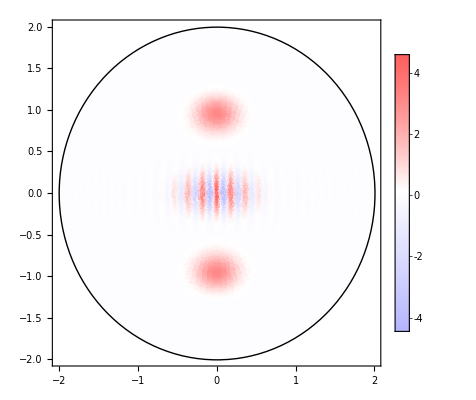

```mathematica
(*Wigner function and Poncaire sections*)
circ=Graphics[{Black,Circle[{0,0},2]},Axes->True,AspectRatio->1];
wigner=Show[ListDensityPlot[datawignerpqkicked,PlotRange->{{-2,2},{-2,2},All},Frame->  True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/15.75(#+15.6)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]],circ]
```

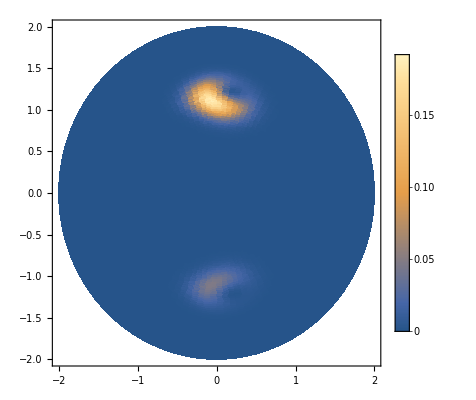

```mathematica
ListDensityPlot[datahusimipqkicked,PlotRange->{{-2,2},{-2,2},All},Frame->True,PlotLegends->Automatic]
```

### Floquet states (driven)

```mathematica
datawignerdriven=Import["src/output/wignertest_driven.dat"];
datahusimidriven=Import["src/output/husimitest_driven.dat"];
```

```mathematica
NN=100;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
J=50;(* Total angular momentum (must coincide the J in the Julia code)*)
Hvol=((2*J+1)/4)*Sum[(π/NN)*(2*π/NN)*Sin[datahusimidriven[[i,1]]]*datahusimidriven[[i,3]],{i,1,Length[datahusimidriven]}](*Volume of the Husimi function*)
Wvol=Sum[(π/NN)*(2*π/NN)*Sin[datawignerdriven[[i,1]]]*datawignerdriven[[i,3]],{i,1,Length[datawignerdriven]}](*Volume of the Wigner function*)
Wneg=Sum[(π/NN)*(2*π/NN)*Sin[datawignerdriven[[i,1]]]*Abs[datawignerdriven[[i,3]]],{i,1,Length[datawignerdriven]}]-Wvol(*Wigner negativity*)
datahusimipqdriven=Table[{qf[datahusimidriven[[i,1]],datahusimidriven[[i,2]]],pf[datahusimidriven[[i,1]],datahusimidriven[[i,2]]],datahusimidriven[[i,3]]},{i,1,Length[datahusimidriven]}];
datawignerpqdriven=Table[{qf[datawignerdriven[[i,1]],datawignerdriven[[i,2]]],pf[datawignerdriven[[i,1]],datawignerdriven[[i,2]]],datawignerdriven[[i,3]]},{i,1,Length[datawignerdriven]}];
```

1.

0.997187

1.10531

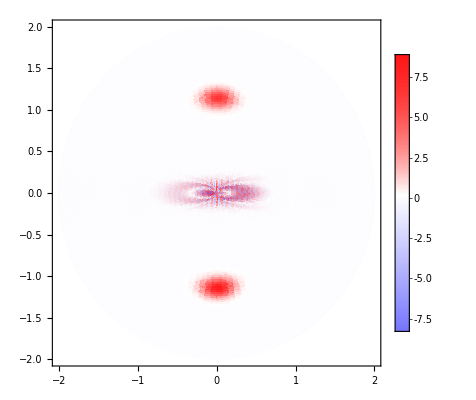

```mathematica
(*Wigner function and Poncaire sections*)
circ=Graphics[{Black,Circle[{0,0},2]},Axes->True,AspectRatio->1];
wigner=Show[ListDensityPlot[datawignerpqdriven,PlotRange->{{-2,2},{-2,2},All},Frame->  True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[1-0.5/15.75(#+15.6)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]],circ]
```

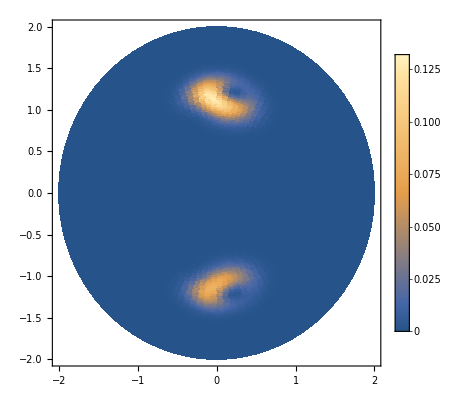

```mathematica
ListDensityPlot[datahusimipqdriven,PlotRange->{{-2,2},{-2,2},All},Frame->True,PlotLegends->Automatic]
```

### Final state adiabatic ramp

```mathematica
dataresonances=Import["src/output/resonances_kicked.dat"];
```

```mathematica
NN=100;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
J=50;(* Total angular momentum (must coincide the J in the Julia code)*)
Hvol=((2*J+1)/4)*Sum[(π/NN)*(2*π/NN)*Sin[datahusimiramp[[i,1]]]*datahusimiramp[[i,3]],{i,1,Length[datahusimiramp]}](*Volume of the Husimi function*)
Wvol=Sum[(π/NN)*(2*π/NN)*Sin[datawignerramp[[i,1]]]*datawignerramp[[i,3]],{i,1,Length[datawignerramp]}](*Volume of the Wigner function*)
Wneg=Sum[(π/NN)*(2*π/NN)*Sin[datawignerramp[[i,1]]]*Abs[datawignerramp[[i,3]]],{i,1,Length[datawignerramp]}]-Wvol(*Wigner negativity*)
datahusimipqramp=Table[{qf[datahusimiramp[[i,1]],datahusimiramp[[i,2]]],pf[datahusimiramp[[i,1]],datahusimiramp[[i,2]]],datahusimiramp[[i,3]]},{i,1,Length[datahusimiramp]}];
datawignerpqramp=Table[{qf[datawignerramp[[i,1]],datawignerramp[[i,2]]],pf[datawignerramp[[i,1]],datawignerramp[[i,2]]],datawignerramp[[i,3]]},{i,1,Length[datawignerramp]}];
```

1.

0.99709

1.1195

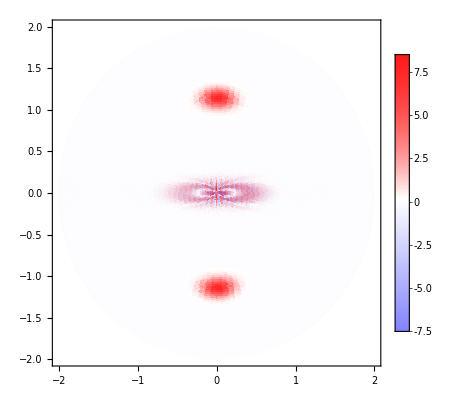

```mathematica
(*Wigner function and Poncaire sections*)

circ=Graphics[{Black,Circle[{0,0},2]},Axes->True,AspectRatio->1];wigner2=Show[ListDensityPlot[datawignerpqramp,PlotRange->{{-2,2},{-2,2},All},Frame->  True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[1-0.5/15.75(#+15.6)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]],circ]
```

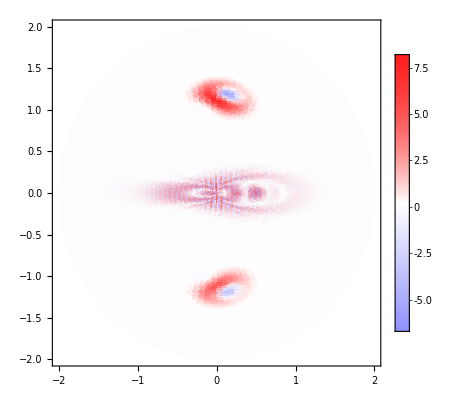

```mathematica
Export["resonance3_RegionI.png",wigner2]
```

resonance3_RegionI.png

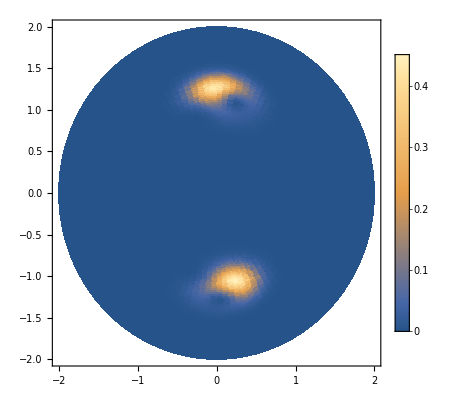

```mathematica
ListDensityPlot[datahusimipqramp,PlotRange->{{-2,2},{-2,2},All},Frame->True,PlotLegends->Automatic]
```

### Fisher Information

```mathematica
dataresonances=Import["src/output/resonances_kicked.dat"];
```

```mathematica
Tres=9.884740906201314;(*T(E_0)*)
DataExpH0=Table[{dataresonances[[i,1]]/Tres,dataresonances[[i,2]]},{i,1,Length[dataresonances]}];
DataQFIJz=Table[{dataresonances[[i,1]]/Tres,dataresonances[[i,3]]},{i,1,Length[dataresonances]}];
DataQFIJy=Table[{dataresonances[[i,1]]/Tres,dataresonances[[i,4]]},{i,1,Length[dataresonances]}];
```

```mathematica
dataresonances[[470]]
```

{4.89,-1.00273,3.60953}

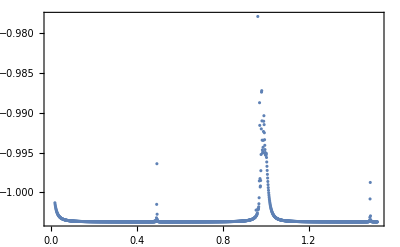

```mathematica
ListPlot[DataExpH0,PlotRange->{All,All},Joined->False,Frame->True,LabelStyle->{Black,15},GridLines->{{},{}},GridLinesStyle->{{Dashed,Red},{}}]
```

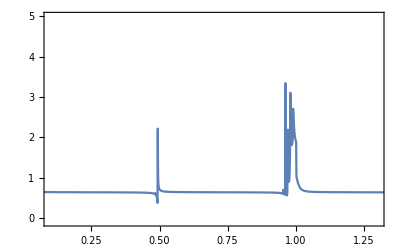

```mathematica
qfi=ListPlot[DataQFIJy,Joined->True,Frame->True,PlotRange->{{0.1,1.3},{-0.1,5}},GridLines->{{1/2,1},{0.6349904662377344}},GridLinesStyle->{{Red,Dashed},{Black,Dashed,Thick}},LabelStyle->{Black,15}]
```

### Cat and mixed state

### Floquet states (kicked)

```mathematica
datwcats=Import["src/output/wignertest_cats.dat"];
dathcats=Import["src/output/husimitest_cats.dat"];
```

```mathematica
NN=100;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
J=20;(* Total angular momentum (must coincide the J in the Julia code)*)
fac=1;
Hvol=((2*J+1)/4)*Sum[(π/NN)*(2*π/NN)*Sin[dathcats[[i,1]]]*dathcats[[i,3]],{i,1,Length[dathcats]}](*Volume of the Husimi function*)
Wvol=Sum[(π/NN)*(2*π/NN)*Sin[datwcats[[i,1]]]*datwcats[[i,3]],{i,1,Length[datwcats]}](*Volume of the Wigner function*)
Wneg=Sum[(π/NN)*(2*π/NN)*Sin[datwcats[[i,1]]]*Abs[datwcats[[i,3]]],{i,1,Length[datwcats]}]-Wvol(*Wigner negativity*)
datah=Table[{qf[dathcats[[i,1]],dathcats[[i,2]]],pf[dathcats[[i,1]],dathcats[[i,2]]],dathcats[[i,3]]},{i,1,Length[dathcats]}];
dataw=Table[{qf[datwcats[[i,1]],datwcats[[i,2]]],pf[datwcats[[i,1]],datwcats[[i,2]]],fac*datwcats[[i,3]]},{i,1,Length[datwcats]}];
```

1.

0.997501

0.910571

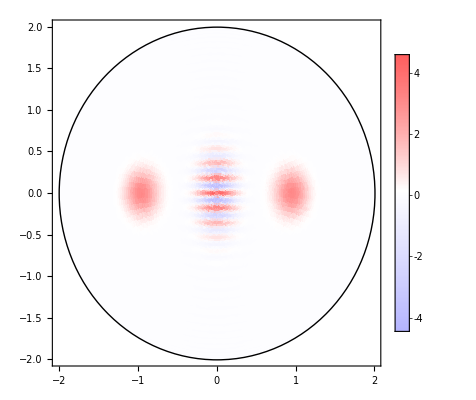

```mathematica
(*Wigner function and Poncaire sections*)
circ=Graphics[{Black,Circle[{0,0},2]},Axes->True,AspectRatio->1];
Show[ListDensityPlot[dataw,PlotRange->{{-2,2},{-2,2},All},Frame->  True,LabelStyle->{Black,24},ColorFunction->(FCo[1-0.5/15.75(#+15.6)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]],circ]
```

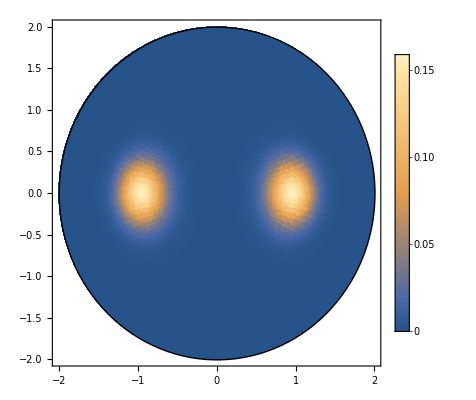

```mathematica
Show[ListDensityPlot[datah,PlotRange->{{-2,2},{-2,2},All},Frame->True,LabelStyle->{Black,25},PlotLegends->Automatic],circ]
```